```mathematica
loadMatlabCell[filePath_String] := Table[Transpose[Import["filePath"][[1,1,x]]],{x,30}]
```

```mathematica
featureYes =loadMatlabCell["/Users/ettoremariotti/Desktop/Semmestre/BCI/Project/BCI-ThoughtRecognition/data_students/EEGyesAmpitudeFeatures.mat"]
```

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed⟦1,1,1⟧ is longer than depth of object.

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed⟦1,1,2⟧ is longer than depth of object.

Import::nffil: File not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1,1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
featureYesMatlab = Import["/Users/ettoremariotti/Desktop/Semmestre/BCI/Project/BCI-ThoughtRecognition/data_students/EEGyesAmpitudeFeatures.mat"];
numFeatYes = Dimensions[featureYesMatlab][[3]]
featureYesRaw =  Table[Transpose[featureYesMatlab[[1,1,x]]],{x,numFeatYes}];
```

```mathematica
featureNoMatlab = Import["/Users/ettoremariotti/Desktop/Semmestre/BCI/Project/BCI-ThoughtRecognition/data_students/EEGnoAmpitudeFeatures.mat"];
numFeatNo = Dimensions[featureNoMatlab][[3]]
featureNoRaw =  Table[Transpose[featureNoMatlab[[1,1,x]]],{x,numFeatNo}];
```

30

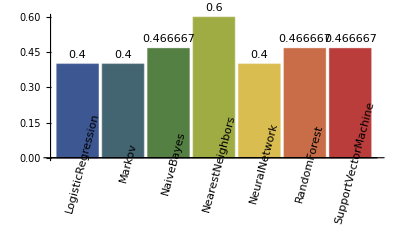

```mathematica
fullFeat = unifyData[featureYesRaw,featureNoRaw];
partFeat = partitionTrainTest[fullFeat,0.75];
showPerformance[partFeat[[1]],partFeat[[2]]]
```

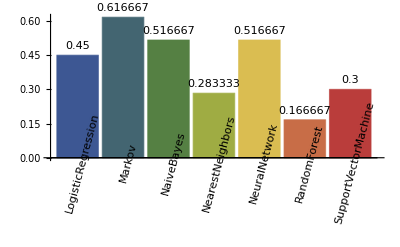

```mathematica
autoML[fullFeat]
```